```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week10

```mathematica
data=Partition[Partition[ReadList["!./laplace 70",Number],3],4048];
```

```mathematica
ListAnimate[Table[ListContourPlot[d,Contours->{90,40,30,20,10,1},RegionFunction->Function[{x,y},Not[(Abs[x]<0.5)&&(Abs[y]<0.5)]],PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{d,data}]]
```

```mathematica
data=Partition[ReadList["!./laplace 200 | awk '/PHI/{print $2, $3, $4}'",Number],3];
```

```mathematica
ListContourPlot[data,Contours->{90,80,70,60,50,40,30,20,10},Epilog->Rectangle[{-.5,-.5},{.5,.5}]]
```

-Graphics-

```mathematica
gdata=Partition[ReadList["!./laplace 70 | awk '/GRAD/{print $2, $3, -$4, -$5}'",Number],4];
```

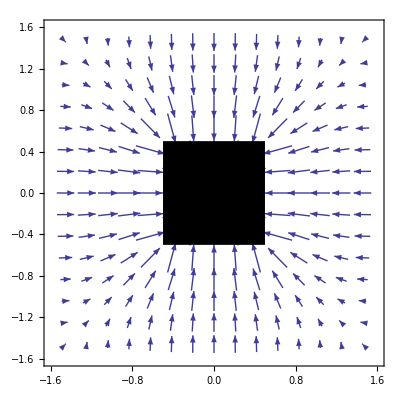

```mathematica
ListVectorPlot[gdata,Epilog->Rectangle[{-.5,-.5},{.5,.5}]]
```

```mathematica
(* the bug I mentioned in class was associated with selecting the values of n in such a way that the original grid has points both on the outer conductor and the inner one. For this to happen n has to be of the form 3*k+1. I fixed the selection below *)
flux=Table[{3.0/(n-1),Partition[ReadList["!./laplace "<>ToString[n]<>" | awk '/flux/{print $2, $3}'",Number],2]},{n,10,91,9}]
```

{{0.333333,{{-656.18,-656.18}}},{0.166667,{{-634.824,-634.824}}},{0.111111,{{-629.194,-629.194}}},{0.0833333,{{-626.729,-626.729}}},{0.0666667,{{-625.383,-625.383}}},{0.0555556,{{-624.549,-624.549}}},{0.047619,{{-623.988,-623.988}}},{0.0416667,{{-623.588,-623.588}}},{0.037037,{{-623.291,-623.291}}},{0.0333333,{{-623.062,-623.062}}}}

res: {{0.333333,-656.18},{0.166667,-634.824},{0.111111,-629.194},{0.0833333,-626.729},{0.0666667,-625.383},{0.0555556,-624.549},{0.047619,-623.988},{0.0416667,-623.588}}

fit: -620.703-62.0044 x-133.371 x^2

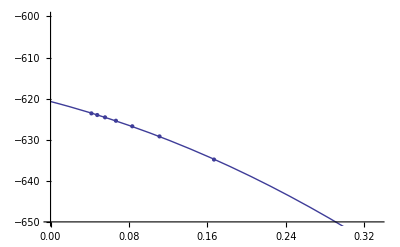

```mathematica
(* this is the data/fit/extrapolation for the flux through the inner countour*)
Block[{res,fit},
res=Table[{flux[[i,1]],flux[[i,2,1,1]]},{i,8}];
Print["res: ",res];
fit=Fit[res,{1,x , x^2},x];
Print["fit: ",fit];
Show[ListPlot[res,PlotRange->{-650,-600}],Plot[fit,{x,0,1}]]
]
```

```mathematica
(* this is the data/fit/extrapolation for the flux through the outer countour*)
Block[{res,fit},
res=Table[{flux[[i,1]],flux[[i,2,1,2]]},{i,8}];
Print["res: ",res];
fit=Fit[res,{1,x , x^2},x];
Print["fit: ",fit];
Show[ListPlot[res,PlotRange->{-650,-600}],Plot[fit,{x,0,1}]]
]
```

res: {{0.333333,-656.18},{0.166667,-634.824},{0.111111,-629.194},{0.0833333,-626.729},{0.0666667,-625.383},{0.0555556,-624.549},{0.047619,-623.988},{0.0416667,-623.588}}

fit: -620.703-62.0044 x-133.371 x^2

-Graphics-